```mathematica
<<getFeigenbaum`
(*f[r_,x_]:=r*x*(1-x);*)
f[r_,x_]:=1-r*x^2;
(*f[r_,x_]:=1-r*Abs[x]^3;*)
(*f[r_,x_]:=r*Sin[π*x];*)

rInv={0,2};

(* Find the Feigenvalues and superstable point of the map in question *)
getFeigenbaum[f,rInv,4,13]
getFeigenbaumPoint[f,rInv,4]
getFeigenbaumConstant[f,rInv,4]
getSuperstablePoints[f,rInv,4]
getScalingFactor[f,rInv,4]
(*TableForm[Table[data[[i,1]]-data[[i-1,1]],{i,1,13}]];*)
(*NumberForm[TableForm[data],9]*)
```

{{0,4},{1.,4},{1.3107,4},{1.38155,4.38568},{1.39695,4.60095},{1.40025,4.65513},{1.40096,4.66611},{1.40111,4.66855},{1.40115,4.66906},{1.40115,4.66917},{1.40115,4.6692},{1.40116,4.6692},{1.40116,4.6692}}

1.40116

4.6692

{0,1.,1.3107,1.38155,1.39695,1.40025,1.40096,1.40111,1.40115,1.40115,1.40115,1.40116}

2.50291

{1.,1.3107,1.38155,1.39695,1.40025,1.40096,1.40111,1.40115,1.40115,1.40115,1.40116}

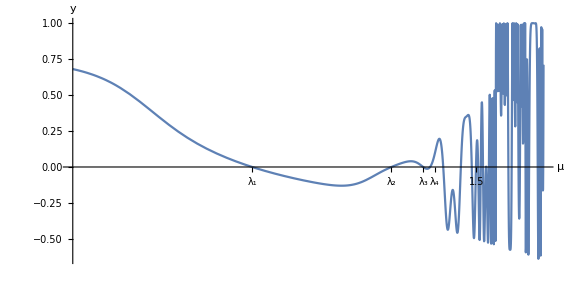

```mathematica
f[r_,x_]:=1-r*x^2;
mu=Drop[getSuperstablePoints[f,{0,2},4],1]
xticks=(Drop[Drop[Charting`FindTicks[{0,1},{0,1}]@@{0,2},{3,3}],{20,20}])~Join~{{mu[[1] ],Subscript[λ,1]},{mu[[2]],Subscript[λ,2]},{mu[[3]],Subscript[λ,3]},{mu[[4]]+0.01,Subscript[λ,4]}};

(* Plot the superstable fixed-point equation whose roots below the Feigenbaum point are the first n superstable points *)
Plot[getIterate[f,r,5][[1]],{r,0.6,1.65},AxesLabel->{μ,y},ImageSize->Large,Ticks->{xticks,Automatic},AspectRatio->1/2]
```

```mathematica
(* check the exponent of the superstable fixed-point equation 
*)
Table[Exponent[getIterate[f,r,n][[1]],r],{n,1,4}]
Table[2^(2^(n-1)-1)-1,{n,1,4}]
```

{0,1,7,127}

{0,1,7,127}

{0,1.,1.3107,1.38155,1.39695,1.40025,1.40096,1.40111,1.40115,1.40115,1.40115,1.40116}

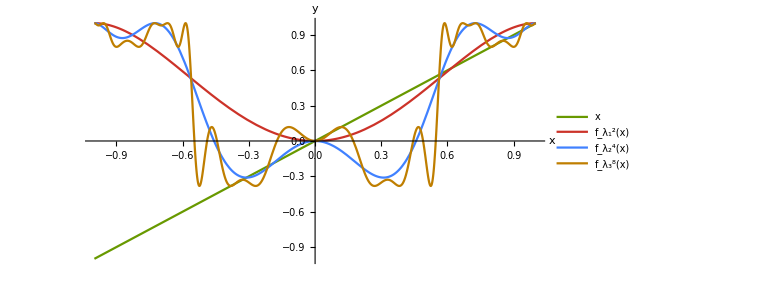

```mathematica
(* Plot some iterates of f where they are superstable *)
l=getSuperstablePoints[f,rInv,4]
Plot[Evaluate[{x}~Join~Table[Nest[f[l[[n]],#1]&,x,2^(n-1)],{n,2,4}]],{x,-1,1},PlotStyle->ColorData[90],PlotLegends->Placed[{"x","f_λ_1^2(x)","f_λ_2^4(x)","f_λ_3^8(x)","f_λ_4^16(x)"},{0.9,0.25}],AxesLabel->{x,y},ImageSize->Large,AspectRatio->1/2]
```

{{2,2.50291},{3,1.92769},{4,1.6903},{5,1.55577},{6,1.46775},{7,1.40512},{8,1.35803},{9,1.32121},{10,1.29156},{11,1.26711},{12,1.24658}}

{{2,4.6692},{3,6.08469},{4,7.2847},{5,8.34444},{6,9.29644},{7,10.1603},{8,10.9497},{9,11.675},{10,12.3448},{11,12.9654},{12,13.5429}}

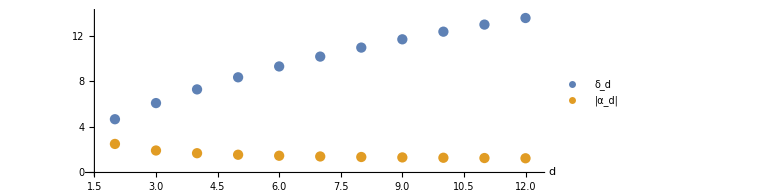

```mathematica
(* Plot the generalized Feigenvalues *)
a=Table[{d,getScalingFactor[1-#1*Abs[#2]^d&,{0,2},2+d]},{d,2,12,1}]
mu=Table[{d,getFeigenbaumConstant[1-#1*Abs[#2]^d&,{0,2},2+d]},{d,2,12,1}]
ListPlot[{mu,a},AxesLabel->{d,None},ImageSize->Large,BaseStyle->{10,ScriptMinSize->3},PlotRange->{{1.5,12.25},{0,14}},AspectRatio->1/3,PlotLegends->Placed[LineLegend[{Subscript[δ, d],"|α_d|"},LegendFunction->(Framed[#,RoundingRadius->0]&),LegendMargins->5],{0.93,0.45}]]
```